Below is the Mathematica code used for calculating values for the measurements PDF f_Y(y), using said values to calculate approximate expectation values for bin counts {ν_i}, using true PDF f_X(x) to calculate exact expectation values for bin counts {μ_j}, and exporting data to CSV files for use in R code.

Defined below are:
	• The true PDF f_X(x), f[x].
	• The Kernel g(x,y), g[x,y].
	• The efficiency ϵ(x), ϵ[x].

```mathematica
f[x_]:= 1/3 PDF[CauchyDistribution[12,2],x]+2/3 PDF[CauchyDistribution[19,2],x];
g[x_,y_]:=PDF[NormalDistribution[-2(Log[Abs[x]+1])^(1/3),2Exp[-Abs[x]/30]],y-x];
ϵ[x_]:=(1-Exp[-Abs[x]/80])^(1/4);
```

Performed below:
	• The sequence of values for x and y from 0 to 30 with step sizes of 0.01 are generated for plotting, xys.
	• The values of the true PDF f_x(x) are calculated for plotting, fxs. 
	• The PDF f_x(x) is integrated across bins of width Δx=1 to produce its corresponding histogram, histxs.

```mathematica
xys =Table[N[x/100],{x,0,3000}];
fxs = N[f[xys]];
histxs = N[Table[∫_(i-1)^i f[x]ⅆx,{i,1,30}]];
```

Performed below:
	• Point-by-point calculations of ∫_(-∞)^∞ f_X(x)ϵ(x)g(x,y)ⅆx to get values of the PDF f_Y(y) for each bin separately, fysd[[i]].
	• The mean for each bin is then found get the histys. 
	• The bins are combined into the values of f_y(y) to be plotted, fys.
The first item takes several minutes to perform.

```mathematica
fysd = Table[Null,{x,1,30}];
For[i=1,i<31,i++,
If[i==24||i==26,
fysd[[i]] = NIntegrate[ExpandAll[f[x]ϵ[x]g[x,N[Table[x/100,{x,(i-1)*100,i*100}]]]],{x,-∞,∞},AccuracyGoal->100,MaxRecursion->800, MinRecursion-> 600],
fysd[[i]] = NIntegrate[ExpandAll[f[x]ϵ[x]g[x,N[Table[x/100,{x,(i-1)*100,i*100}]]]],{x,-∞,∞}]]];
histys =Table[Mean[fysd[[i]]],{i,1,30}];
seq =Table[x,{x,2,101}];
fys = Flatten[Join[{fysd[[1]]},Table[fysd[[i]][[seq]],{i,2,30}]]];
```

Plotting fxs, fys, histxs, and histys.

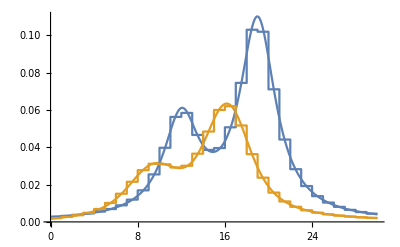

```mathematica
Show[ListLinePlot[{Transpose[{xys,fxs}],Transpose[{xys,fys}]}],
ListStepPlot[{Transpose[{Table[x,{x,0,29}],histxs}],Transpose[{Table[x,{x,0,29}],histys}]}]]
```

Generating column contents for the tibble exp_hist to be used for plotting histxs and histxy in R.

```mathematica
hbinl = Join[Table[x,{x,0,29}],Table[x,{x,0,29}]];
hbinh = Join[Table[x,{x,1,30}],Table[x,{x,1,30}]];
hcountl = Join[{0},histxs[[Table[x,{x,1,29}]]],
{0},histys[[Table[x,{x,1,29}]]]];
hcount = Join[histxs,histys];
treat = Join[Table["not folded",{x,1,30}],Table["folded",{x,1,30}]];
```

Saving plotting data to their appropriate files.

```mathematica
SetDirectory[NotebookDirectory[]];
Export["fyEstimate.csv",
Transpose[{PrependTo[xys,Y],PrependTo[fys,Density]}]];
Export["histExpected.csv",
Transpose[{PrependTo[hbinl,binLow],PrependTo[hbinh,binHigh],
PrependTo[hcountl,CountsL],PrependTo[hcount,Counts],
PrependTo[treat,Treatment]}]];
```